```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/charlie/research/collins2018/mathematica

```mathematica
<<ErrorBarLogPlots`
```

```mathematica
avk = 0.57
avp=0.12
```

0.57

0.12

## Read and interpolate DSS collinear fragmentation functions.

```mathematica
DSShplus= ReadList["fragmentationpiplus.dat",Real,RecordLists-> True];
DSShminus= ReadList["fragmentationpiminus.dat",Real,RecordLists-> True];
```

```mathematica
uhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,3]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}]
dhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,4]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
shplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,5]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
ubhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,6]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
dbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,7]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
sbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,8]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[{{0.010098, 0.989902}, {1., 89.11}}, <>]

```mathematica
uhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,3]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}]
dhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,4]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
shminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,5]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
ubhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,6]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
dbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,7]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
sbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,8]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[{{0.010098, 0.989902}, {1., 89.11}}, <>]

InterpolatingFunction::dmval: Input value {0.0100202,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

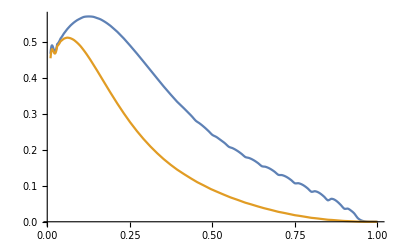

```mathematica
Plot[{z uhplus[z,3.],z dhplus[z,3.]},{z,0.01,1}]
```

## D_1

```mathematica
(*2005 fit Appendix A.1 [hep-ph/0501196]*)
Clear[avp];
avp=0.2;
(* fragmentation*)
D1uTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1ubarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]


D1u[pion_,z_,Q2_ ]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]]  
D1d[pion_,z_,Q2_ ]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]]  
D1ubar[pion_,z_,Q2_ ]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]]  
D1dbar[pion_,z_,Q2_ ]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]]  
D1s[pion_,z_,Q2_ ]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]]  
D1sbar[pion_,z_,Q2_ ]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

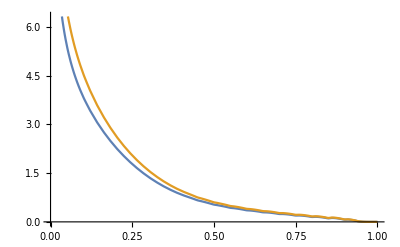

```mathematica
Plot[{D1u["pi+",z,1.],D1d["pi-",z,1.]},{z,0,1}]
```

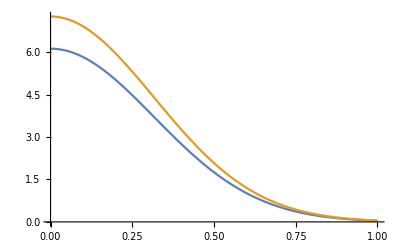

```mathematica
Plot[{D1uTMD["pi+",0.1,1.,pt],D1dTMD["pi-",0.1,1.,pt]},{pt,0,1}]
```

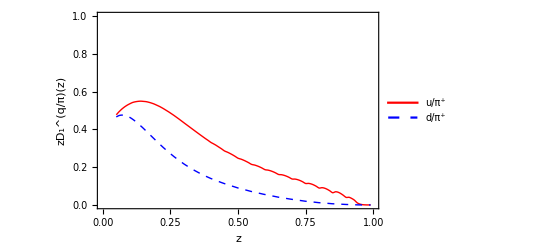

```mathematica
D1plot =Plot[{x D1u["pi+",x,2.4],x D1d["pi+",x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zD_1^(q/π)(z)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.7}]]
```

## Read and interpolate Soffer Bound collinear distribution functions.

```mathematica
sb= ReadList["SofferBound.dat",Real,RecordLists-> True];
```

```mathematica
sb1u=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,3]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1d=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,4]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1s=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,5]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1ubar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,6]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1dbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,7]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1sbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,8]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction::dmval: Input value {0.0100202,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

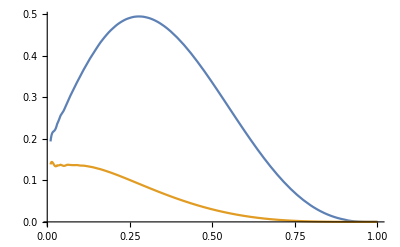

```mathematica
Plot[{x*sb1u[x,1.],x*sb1d[x,1.]},{x,0.01,1}]
```

## h_1

```mathematica
Clear[NuT,NdT,alphaT,betaT];
NuT=0.37;
NdT=-1.000;
alphaT=0.75;
betaT=2.35;

(* Transversity function with DGLAP Evolution*)
h1u[x_,Q2_]:=(NuT x^alphaT (1-x)^betaT(alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT))) sb1u[x,Q2];
h1d[x_,Q2_]:=(NdT x^alphaT (1-x)^betaT (alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT)))sb1d[x,Q2];

h1uTMD[x_,Q2_,kt_]:=h1u[x,Q2]1/(π avk) Exp[-kt^2/avk];
h1dTMD[x_,Q2_,kt_]:=h1d[x,Q2]1/(π avk) Exp[-kt^2/avk];


year = 2018;
width = 57;
MyLabel= StringForm["`` fit ⟨k_⊥^2⟩ = 0.`` (GeV^2).",year,width]
```

2018 fit ⟨k_⊥^2⟩ = 0.57 (GeV^2).

InterpolatingFunction::dmval: Input value {0.0010202,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

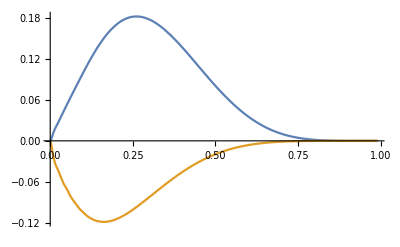

```mathematica
Plot[{x h1u[x,1.], x h1d[x,1.]},{x,0.001,0.99}]
```

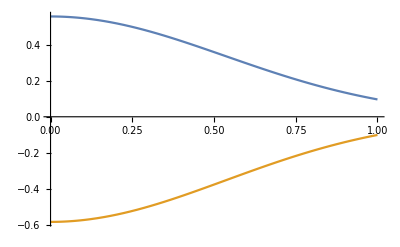

```mathematica
Plot[{h1uTMD[0.1,1.,kt],h1dTMD[0.1,1.,kt]},{kt,0,1}]
```

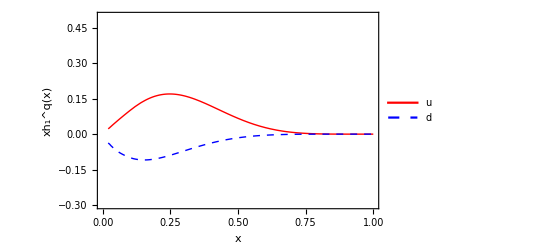

```mathematica
h1plot =Plot[{x h1u[x,2.4],x h1d[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.3,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_1^q(x)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

## H_1^⊥

```mathematica
Clear[MC,NCfav,NCunf,alphaC,betaC, Mh];
MC=Sqrt[0.30];
NCfav=0.52;
NCunf=-0.43;
alphaC=0.73;
betaC=0.0000001;
Mh = 0.139;

(*Collins function with DGLAP Evolution*)
H1perpFavHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));
H1perpUnfHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));

H1perpFavFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);
H1perpUnfFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);

H1perpFavTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1u["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];
H1perpUnfTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCunf )D1d["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];


year = 2018;
width = 12;
MyLabel= StringForm["`` fit ⟨p_⊥^2⟩ = 0.`` (GeV^2).",year,width]

H1perpFirstMoment[quark_,pion_,x_,Q2_] := If[(quark == "u" && pion == "pi+") || (quark == "bard" && pion == "pi+") || (quark == "d" && pion == "pi-") || (quark == "baru" && pion == "pi-"),H1perpFavFirstMoment[x,Q2],H1perpUnfFirstMoment[x,Q2]]
```

2018 fit ⟨p_⊥^2⟩ = 0.12 (GeV^2).

```mathematica
H1perpFavFirstMoment[.1,2.4]
```

5.72047

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

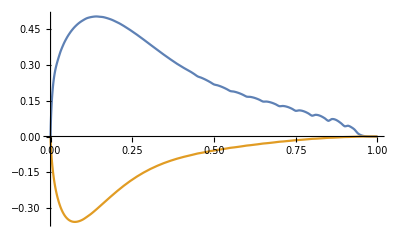

```mathematica
Plot[{H1perpFavHalfMoment[z,1.],H1perpUnfHalfMoment[z,1.]},{z,0,1}]
```

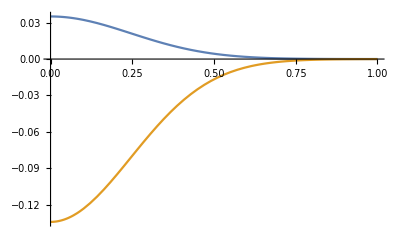

```mathematica
Plot[{H1perpFavTMD[0.1,1.,pt],H1perpUnfTMD[0.1,1.,pt]},{pt,0,1}]
```

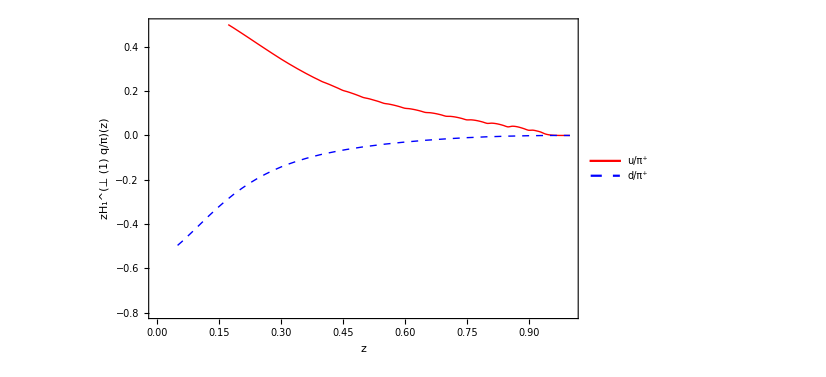

```mathematica
H1perpplot =Plot[{x H1perpFavFirstMoment[x,2.4],x H1perpUnfFirstMoment[x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.8,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zH_1^(⊥ (1) q/π)(z)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.3}]]
```

```mathematica
dataH1perpFavFirstMomentTable = Table[{z,H1perpFavFirstMoment[z,2.4]},{z,0.02,0.98,0.01}];
dataH1perpUnfFirstMomentTable = Table[{z, H1perpUnfFirstMoment[z,2.4]},{z,0.02,0.98,0.01}];
```

```mathematica
datah1uTable = Table[{x,h1u[x,2.4]},{x,0.02,0.98,0.01}];
datah1dTable = Table[{x,h1d[x,2.4]},{x,0.02,0.98,0.01}];
```

```mathematica
H1perpFavFirstMomentGuess[z_]=Nfav * z^c*(1.-z)^d
```

Nfav z^c (1.-z)^d

```mathematica
H1perpUnfFirstMomentGuess[z_]=Nunf * z^c*(1.-z)^d
```

Nunf z^c (1.-z)^d

```mathematica
h1uGuess[x_]=Nu * x^au*(1.-x)^bu
h1dGuess[x_]=-Nd * x^ad*(1.-x)^bd
```

Nu x^au (1.-x)^bu

-Nd x^ad (1.-x)^bd

```mathematica
h1uGuessFit=NonlinearModelFit[datah1uTable,{h1uGuess[x]},{Nu,au,bu},{x}]
```

FittedModel[2.71035 (1.-x)^3.8386 x^0.239414]

```mathematica
h1dGuessFit=NonlinearModelFit[datah1dTable,{h1dGuess[x]},{Nd,ad,bd},{x}]
```

FittedModel[-(1.32577 (1.-x)^5.10632)/x^0.106715]

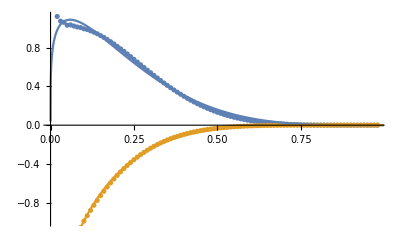

```mathematica
Show[ListPlot[{datah1uTable,datah1dTable}],Plot[{h1uGuessFit [x],h1dGuessFit[x]},{x,0,1}]]
```

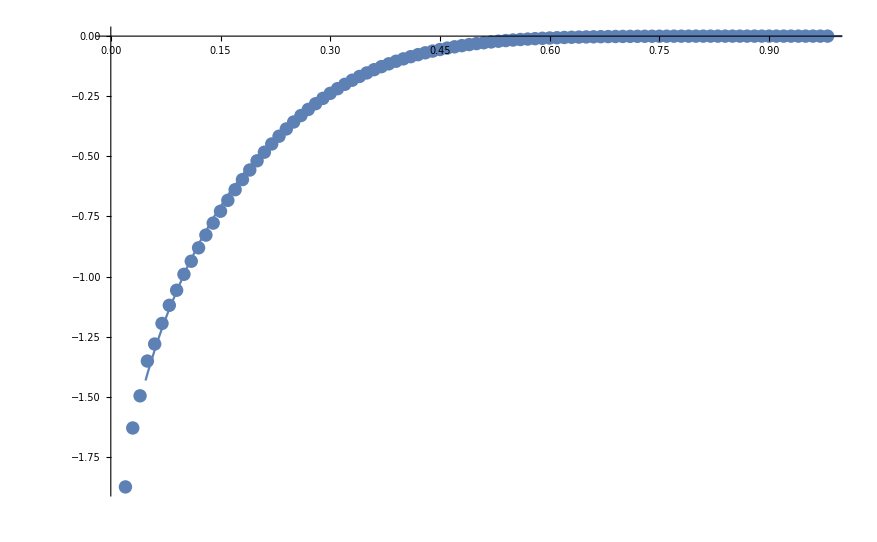

```mathematica
Show[ListPlot[{datah1dTable}],Plot[{h1dGuessFit[x]},{x,0,1}]]
```

```mathematica
allH1perpFirstMomentGuessData=Join[{1,Sequence@@#}&/@dataH1perpFavFirstMomentTable,{2,Sequence@@#}&/@dataH1perpUnfFirstMomentTable];
```

```mathematica
H1perpFirstMomentGuess[index_,z_]:=KroneckerDelta[index-1] H1perpFavFirstMomentGuess[z]+KroneckerDelta[index-2] H1perpUnfFirstMomentGuess[z]
```

```mathematica
H1perpFirstMomentGuessFit = NonlinearModelFit[allH1perpFirstMomentGuessData,H1perpFirstMomentGuess[index,z],{Nfav,Nunf,c,d},{index,z}]
```

FittedModel[(0.636296 (1.-z)^2.24624 1-index)/z^1.03066-(0.50632 (1.-z)^2.24624 2-index)/z^1.03066]

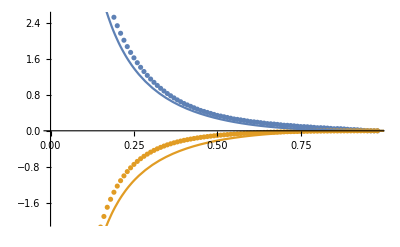

```mathematica
Show[ListPlot[{dataH1perpFavFirstMomentTable,dataH1perpUnfFirstMomentTable}],Plot[{H1perpFirstMomentGuessFit [1,z],H1perpFirstMomentGuessFit [2,z]},{z,0,1}]]
```